# 数据

## 鸢尾花数据集

```mathematica
irisData=ExampleData[{"MachineLearning","FisherIris"},"Data"];
{sepalLength,sepalWidth,petalLength,petalWidth}=Table[irisData[[i,1,j]],{j,1,4},{i,1,150}];
```

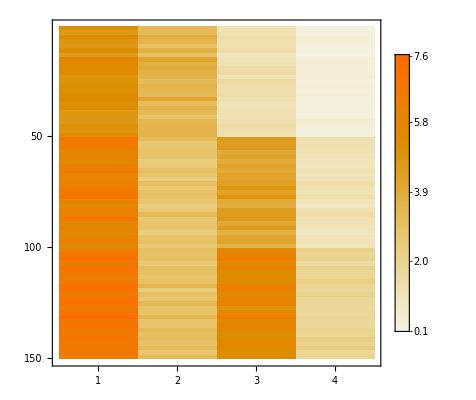

```mathematica
MatrixPlot[Transpose@{sepalLength,sepalWidth,petalLength,petalWidth},AspectRatio->1,PlotTheme->"Detailed"]
```

## 核密度估计

```mathematica
PDF[SmoothKernelDistribution[#],x]&/@{sepalLength,sepalWidth,petalLength,petalWidth};
"μ= "<>ToString[Mean[#]]<>", σ= "<>ToString[StandardDeviation[#]]&/@{sepalLength,sepalWidth,petalLength,petalWidth};
Plot[%%,{x,-1,9},Filling->Axis,PlotRange->All,PlotLegends->{"Sepal Length","Sepal Width","Petal Length","Petal Width"},AspectRatio->1/3,ImageSize->Large,PlotTheme->"Detailed",PlotLabels->Callout[%,Above]]
```

-Graphics-

## 协方差矩阵和相关性系数矩阵

## 整体

```mathematica
covarianceMatrix=Covariance@Transpose@{sepalLength,sepalWidth,petalLength,petalWidth}
```

{{0.685694,-0.042434,1.27432,0.516271},{-0.042434,0.189979,-0.329656,-0.121639},{1.27432,-0.329656,3.11628,1.29561},{0.516271,-0.121639,1.29561,0.581006}}

```mathematica
correlationMatrix=Correlation@Transpose@{sepalLength,sepalWidth,petalLength,petalWidth}
```

{{1.,-0.11757,0.871754,0.817941},{-0.11757,1.,-0.42844,-0.366126},{0.871754,-0.42844,1.,0.962865},{0.817941,-0.366126,0.962865,1.}}

```mathematica
{MatrixPlot[covarianceMatrix,ColorFunction->"ThermometerColors",PlotLabel->"Covariance Matrix",Mesh->All,Epilog->{MapIndexed[Text[Round[#1,0.01](*保留两位小数*),{#2[[2]]-0.5,Length[covarianceMatrix]-#2[[1]]+0.5}(*数字放置位置*)]&,covarianceMatrix,{2}]},PlotTheme->"Detailed"],MatrixPlot[correlationMatrix,ColorFunction->"ThermometerColors",PlotLabel->"Correlation Matrix",Mesh->All,Epilog->{MapIndexed[Text[Round[#1,0.01](*保留两位小数*),{#2[[2]]-0.5,Length[covarianceMatrix]-#2[[1]]+0.5}(*数字放置位置*)]&,correlationMatrix,{2}]},PlotTheme->"Detailed"]}//GraphicsRow[#,ImageSize->Large]&
```

-Graphics-

## 分类

```mathematica
{setosaData,versicolorData,virginicaData}=Transpose[{sepalLength,sepalWidth,petalLength,petalWidth}][[#]]&/@{1;;50,51;;100,101;;150};
```

```mathematica
Covariance/@{setosaData,versicolorData,virginicaData};
{MatrixPlot[%[[1]],ColorFunction->"ThermometerColors",PlotLabel->"C_1, setosa",Mesh->All,Epilog->{MapIndexed[Text[Round[#1,0.01](*保留两位小数*),{#2[[2]]-0.5,Length[%[[1]]]-#2[[1]]+0.5}(*数字放置位置*)]&,%[[1]],{2}]},PlotTheme->"Detailed"],MatrixPlot[%[[2]],ColorFunction->"ThermometerColors",PlotLabel->"C_2, versicolor",Mesh->All,Epilog->{MapIndexed[Text[Round[#1,0.01](*保留两位小数*),{#2[[2]]-0.5,Length[%[[2]]]-#2[[1]]+0.5}(*数字放置位置*)]&,%[[2]],{2}]},PlotTheme->"Detailed"],MatrixPlot[%[[3]],ColorFunction->"ThermometerColors",PlotLabel->"C_3, virginica",Mesh->All,Epilog->{MapIndexed[Text[Round[#1,0.01](*保留两位小数*),{#2[[2]]-0.5,Length[%[[3]]]-#2[[1]]+0.5}(*数字放置位置*)]&,%[[3]],{2}]},PlotTheme->"Detailed"]}//GraphicsRow[#,ImageSize->600]&
```

-Graphics-

```mathematica
Correlation/@{setosaData,versicolorData,virginicaData};
{MatrixPlot[%[[1]],ColorFunction->"ThermometerColors",PlotLabel->"C_1, setosa",Mesh->All,Epilog->{MapIndexed[Text[Round[#1,0.01](*保留两位小数*),{#2[[2]]-0.5,Length[%[[1]]]-#2[[1]]+0.5}(*数字放置位置*)]&,%[[1]],{2}]},PlotTheme->"Detailed"],MatrixPlot[%[[2]],ColorFunction->"ThermometerColors",PlotLabel->"C_2, versicolor",Mesh->All,Epilog->{MapIndexed[Text[Round[#1,0.01](*保留两位小数*),{#2[[2]]-0.5,Length[%[[2]]]-#2[[1]]+0.5}(*数字放置位置*)]&,%[[2]],{2}]},PlotTheme->"Detailed"],MatrixPlot[%[[3]],ColorFunction->"ThermometerColors",PlotLabel->"C_3, virginica",Mesh->All,Epilog->{MapIndexed[Text[Round[#1,0.01](*保留两位小数*),{#2[[2]]-0.5,Length[%[[3]]]-#2[[1]]+0.5}(*数字放置位置*)]&,%[[3]],{2}]},PlotTheme->"Detailed"]}//GraphicsRow[#,ImageSize->600]&
```

-Graphics-

## 数据分解

## QR 分解

```mathematica
String2Pic[string_]:=Rasterize[Text[string],RasterSize->100,ImageSize->50](*将符号转化为图片*)
```

```mathematica
QRMatrixPlot[matrix_]:=Module[{QMatrix,RMatrix,plots},
{QMatrix,RMatrix}=QRDecomposition@matrix;
plots=MatrixPlot[#,AspectRatio->1,ImageSize->Small,PlotTheme->"Minimal"]&/@{matrix,Transpose@QMatrix,RMatrix};
GraphicsRow[{plots[[1]],String2Pic["="],plots[[2]],String2Pic["@"],plots[[3]]},ImageSize->500]
]
```

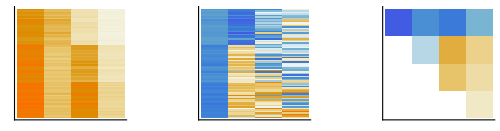

```mathematica
QRMatrixPlot[Transpose@{sepalLength,sepalWidth,petalLength,petalWidth}]
```

## Cholesky 分解

```mathematica
irisGram=Transpose@#.#&@Transpose@{sepalLength,sepalWidth,petalLength,petalWidth}
```

{{5223.85,2673.43,3483.76,1128.14},{2673.43,1430.4,1674.3,531.89},{3483.76,1674.3,2582.71,869.11},{1128.14,531.89,869.11,302.33}}

```mathematica
CholeskyMatrixPlot[matrix_]:=Module[{plots},
plots=MatrixPlot[#,PlotTheme->"Minimal",AspectRatio->1,ImageSize->Small]&/@{matrix,Transpose@#,#}&@CholeskyDecomposition[matrix];
GraphicsRow[{plots[[1]],String2Pic["="],plots[[2]],String2Pic["@"],plots[[3]]},ImageSize->500]
]
```

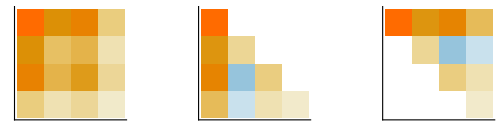

```mathematica
CholeskyMatrixPlot[irisGram]
```

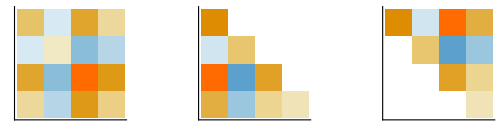

```mathematica
CholeskyMatrixPlot[covarianceMatrix]
```

## 特征值分解

```mathematica
EigenMatrixPlot[matrix_]:=Module[{plots},
plots=MatrixPlot[#,AspectRatio->1,PlotTheme->"Minimal",ImageSize->Small]&/@{matrix,#[[2]],DiagonalMatrix@#[[1]],Transpose@#[[2]]}&@Eigensystem[matrix];
GraphicsRow[{plots[[1]],String2Pic["="],plots[[2]],String2Pic["@"],plots[[3]],String2Pic["@"],plots[[4]]},ImageSize->500]
]
```

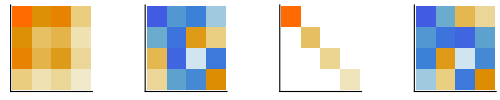

```mathematica
EigenMatrixPlot[irisGram]
```

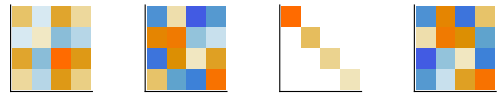

```mathematica
EigenMatrixPlot[covarianceMatrix]
```

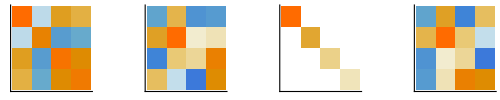

```mathematica
EigenMatrixPlot[correlationMatrix]
```

## 奇异值分解

```mathematica
SVDMatrixPlot[matrix_]:=Module[{UMatrix,SMatrix,Vmatrix,plots},
{UMatrix,SMatrix,Vmatrix}=SingularValueDecomposition[matrix,MatrixRank[matrix]];(*紧凑型SVD分解*)
plots=MatrixPlot[#,AspectRatio->1,ImageSize->Small,PlotTheme->"Minimal"]&/@{matrix,UMatrix,SMatrix,Transpose@Vmatrix};
GraphicsRow[{plots[[1]],String2Pic["="],plots[[2]],String2Pic["@"],plots[[3]],String2Pic["@"],plots[[4]]},ImageSize->500]
]
```

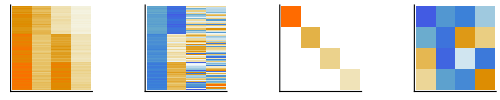

```mathematica
SVDMatrixPlot[Transpose@{sepalLength,sepalWidth,petalLength,petalWidth}]
```

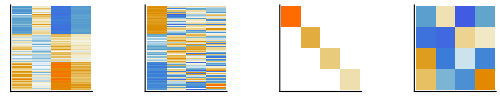

```mathematica
#-Mean[#]&(*中心化数据*)/@{sepalLength,sepalWidth,petalLength,petalWidth}//Transpose//SVDMatrixPlot
```

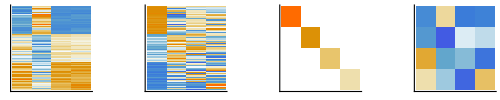

```mathematica
Standardize(*标准化数据*)/@{sepalLength,sepalWidth,petalLength,petalWidth}//Transpose//SVDMatrixPlot
```

## 机器学习

## 无监督学习

### 聚类

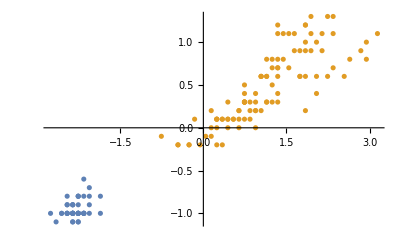

```mathematica
ListPlot@FindClusters@Transpose[#-Mean[#]&(*中心化数据*)/@{petalLength,petalWidth}]
```

### 降维

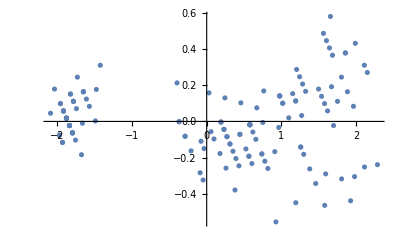

```mathematica
ListPlot@DimensionReduce[Transpose[#-Mean[#]&(*中心化数据*)/@{petalLength,petalWidth}],2]
```

## 有监督学习

### 回归

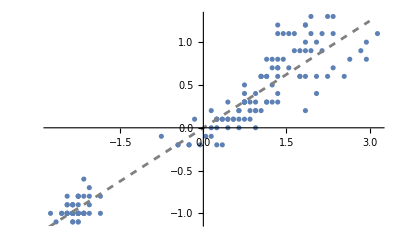

```mathematica
Show[ListPlot@#,Plot[Evaluate@Fit[#,{1,x},x],{x,-3,3},PlotStyle->{Gray,Dashed}]]&@Transpose[#-Mean[#]&(*中心化数据*)/@{petalLength,petalWidth}]
```

### 分类

```mathematica
c=Classify[ExampleData[{"MachineLearning","FisherIris"},"TrainingData"]]
```

ClassifierFunction[…]

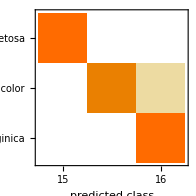
Classifier Measurements
Classifier method | LogisticRegression
Number of test examples | 45
Accuracy | (97.82.2) %
Accuracy baseline | (33.7.) %
Geometric mean of probabilities | 0.946 ± 0.038
Mean cross entropy | 0.0552 ± 0.04
Single evaluation time | 3.27 ms/example
Batch evaluation speed | 7.87 examples/ms
-Graphics- |

```mathematica
cm=ClassifierMeasurements[c,ExampleData[{"MachineLearning","FisherIris"},"TestData"]]
```